## Preamble

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
?gPolygon
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
(* <<TestAlgebra`  *)
<<Geometry`
```

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## DivisorsByBox

## Overview

```mathematica
Map[#&,IntegerPartitions[5]]
Map[#&,Map[#+1&,IntegerPartitions[5]]]
Map[Times@@#&,Map[#+1&,IntegerPartitions[5]]]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

{{6},{5,2},{4,3},{4,2,2},{3,3,2},{3,2,2,2},{2,2,2,2,2}}

{6,10,12,16,18,24,32}

## tmp-1

```mathematica
Map[#&,IntegerPartitions[6]]
GroupBy[Map[#&,IntegerPartitions[6]],Length]
Values[GroupBy[Map[#&,IntegerPartitions[6]],Length]]
Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]
Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

<|1→{{6}},2→{{5,1},{4,2},{3,3}},3→{{4,1,1},{3,2,1},{2,2,2}},4→{{3,1,1,1},{2,2,1,1}},5→{{2,1,1,1,1}},6→{{1,1,1,1,1,1}}|>

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

{{7},{6,2},{5,3},{4,4},{5,2,2},{4,3,2},{3,3,3},{4,2,2,2},{3,3,2,2},{3,2,2,2,2},{2,2,2,2,2,2}}

{7,12,15,16,20,24,27,32,36,48,64}

```mathematica
fDivisorsByBox[n_]:=Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[n]],Length]],1]]
Table[fDivisorsByBox[k],{k,10}]//TableForm
```

2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3 | 4 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 6 | 8 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 8 | 9 | 12 | 16 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 | 10 | 12 | 16 | 18 | 24 | 32 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 12 | 15 | 16 | 20 | 24 | 27 | 32 | 36 | 48 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8 | 14 | 18 | 20 | 24 | 30 | 32 | 36 | 40 | 48 | 54 | 64 | 72 | 96 | 128 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9 | 16 | 21 | 24 | 25 | 28 | 36 | 40 | 45 | 48 | 48 | 60 | 64 | 72 | 81 | 80 | 96 | 108 | 128 | 144 | 192 | 256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 | 18 | 24 | 28 | 30 | 32 | 42 | 48 | 54 | 50 | 60 | 64 | 56 | 72 | 80 | 90 | 96 | 108 | 96 | 120 | 128 | 144 | 162 | 160 | 192 | 216 | 256 | 288 | 384 | 512 |  |  |  |  |  |  |  |  |  |  |  | 
11 | 20 | 27 | 32 | 35 | 36 | 36 | 48 | 56 | 63 | 60 | 72 | 75 | 80 | 64 | 84 | 96 | 108 | 100 | 120 | 135 | 128 | 144 | 112 | 144 | 160 | 180 | 192 | 216 | 243 | 192 | 240 | 256 | 288 | 324 | 320 | 384 | 432 | 512 | 576 | 768 | 1024

{{2},{3,4},{4,6,8},{5,8,9,12,16},{6,10,12,16,18,24,32},{7,12,15,16,20,24,27,32,36,48,64},{8,14,18,20,24,30,32,36,40,48,54,64,72,96,128},{9,16,21,24,25,28,36,40,45,48,48,60,64,72,81,80,96,108,128,144,192,256},{10,18,24,28,30,32,42,48,54,50,60,64,56,72,80,90,96,108,96,120,128,144,162,160,192,216,256,288,384,512},{11,20,27,32,35,36,36,48,56,63,60,72,75,80,64,84,96,108,100,120,135,128,144,112,144,160,180,192,216,243,192,240,256,288,324,320,384,432,512,576,768,1024}}

## tmp-2

```mathematica
sortByNumberOfDivisors[ls_]:=Times@@(ls+1)
fNumberOfDivisorsByPartition[n_]:=Map[Times@@(#+1)&,SortBy[IntegerPartitions[n],sortByNumberOfDivisors[#]&]]
Table[fNumberOfDivisorsByPartition[k],{k,13,13}]
```

{{14,26,36,44,48,50,54,56,66,80,88,90,90,96,98,108,120,120,126,128,140,144,144,150,160,160,162,168,192,210,216,216,216,224,240,250,252,256,270,280,288,288,288,288,300,320,336,360,378,384,384,400,432,448,450,480,480,486,504,512,512,540,576,576,600,640,648,672,720,768,768,800,810,864,864,896,960,972,1024,1080,1152,1152,1280,1296,1440,1458,1536,1536,1728,1920,1944,2048,2304,2560,2592,3072,3456,4096,4608,6144,8192}}

## tmp-3

```mathematica
num= 48
fac=FactorInteger[num]
len=Length[fac]
Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}]
set=Flatten[Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}],1]
SetPartitions[set]
Map[Sort[#]&,SetPartitions[set]]
tmp=Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
Map[#&,tmp]
Map[Map[Times@@#&,#]&,tmp]
Map[ReverseSort[#]&,Map[Map[Times@@#&,#]&,tmp]-1]
```

```mathematica
nnFactorList[n_]:=Module[
{fac,len,tab,set,ssp,spt,lst},
fac=FactorInteger[n];
len=Length[fac];
tab=Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}];
set=Flatten[tab,1];
ssp=SetPartitions[set];
spt=Map[Sort[#]&,ssp]//DeleteDuplicates;
lst=Map[Map[Times@@#&,#]&,spt];
lst
]
```

```mathematica
lst=nnFactorList[96];
lst;
lst//Length;
Map[ReverseSort[#]&,lst-1]
```

{{95},{47,1},{23,3},{11,7},{15,5},{31,2},{23,1,1},{11,3,1},{7,5,1},{15,2,1},{5,3,3},{7,3,2},{11,1,1,1},{5,3,1,1},{7,2,1,1},{3,3,2,1},{5,1,1,1,1},{3,2,1,1,1},{2,1,1,1,1,1}}

```mathematica
nnFactorPartitions[set_]:=Module[
{lst},
lst=SetPartitions[set];
lst=Sort[#]&/@lst;
lst=lst//DeleteDuplicates;
lst
]
```

```mathematica
nnFactorPartitions[{p,p,p,p,q,r}];
```

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==5&]//Length
```

4

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==3&]/.{p:>2,q:>3,r:>5}
```

{{{2},{2},{2,2,3,5}},{{2},{2,2},{2,3,5}},{{2},{3,5},{2,2,2}},{{2},{5},{2,2,2,3}},{{2},{2,5},{2,2,3}},{{2},{2,3},{2,2,5}},{{2},{3},{2,2,2,5}},{{2,2},{2,2},{3,5}},{{5},{2,2},{2,2,3}},{{2,2},{2,3},{2,5}},{{3},{2,2},{2,2,5}},{{5},{2,3},{2,2,2}},{{3},{2,5},{2,2,2}},{{3},{5},{2,2,2,2}}}

```mathematica
Times@@(IntegerPartitions[10][[6]]+1)
8 3 2
```

48

48

```mathematica
IntegerPartitions[10]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{5,1,1,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1},{4,3,1,1,1},{4,2,2,2},{4,2,2,1,1},{4,2,1,1,1,1},{4,1,1,1,1,1,1},{3,3,3,1},{3,3,2,2},{3,3,2,1,1},{3,3,1,1,1,1},{3,2,2,2,1},{3,2,2,1,1,1},{3,2,1,1,1,1,1},{3,1,1,1,1,1,1,1},{2,2,2,2,2},{2,2,2,2,1,1},{2,2,2,1,1,1,1},{2,2,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
SortBy[IntegerPartitions[8],sortByNumberOfDivisors[#]&]
```

{{8},{7,1},{6,2},{5,3},{4,4},{6,1,1},{5,2,1},{4,3,1},{4,2,2},{3,3,2},{5,1,1,1},{4,2,1,1},{3,3,1,1},{3,2,2,1},{4,1,1,1,1},{2,2,2,2},{3,2,1,1,1},{2,2,2,1,1},{3,1,1,1,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
FactorInteger[768]
```

{{2,8},{3,1}}

```mathematica
fP[n_]:=PartitionsP[n]-PartitionsP[n-1]
Table[fP[k],{k,3,15}]
```

{1,2,2,4,4,7,8,12,14,21,24,34,41}

```mathematica
2^29 3^3 5^2
IntegerName[2^29 3^3 5^2]
Divisors[2^29 3^3 5^2]//Length
```

362387865600

362 billion 387 million 865 thousand 600

360

```mathematica
2^8 3^7 5^4
IntegerName[2^8 3^7 5^4]
Divisors[2^8 3^7 5^4]//Length
```

349920000

349 million 920 thousand

360

```mathematica
Table[IntegerPartitions[6,{k}],{k,1,6}]
```

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

```mathematica
12 2 3 5
```

360

```mathematica
num1=2^19 5^4 7^4 13^1
IntegerName[num1]
Divisors[num1]//Length
Divisors[num1];
```

10227875840000

10 trillion 227 billion 875 million 840 thousand

1000

```mathematica
1260 64 99
FactorInteger[1260]
Divisors[1260]//Length
Divisors[32 99]//Length
Divisors[1260 64 99]//Length
```

7983360

{{2,2},{3,2},{5,1},{7,1}}

36

36

360

```mathematica
FactorInteger[30][[All,2]]
```

{1,1,1}

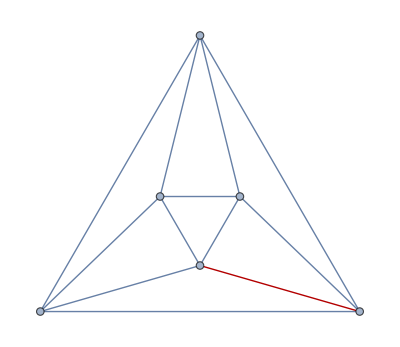
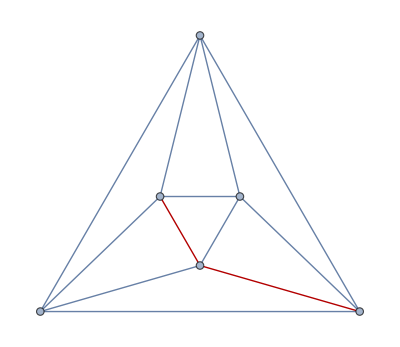
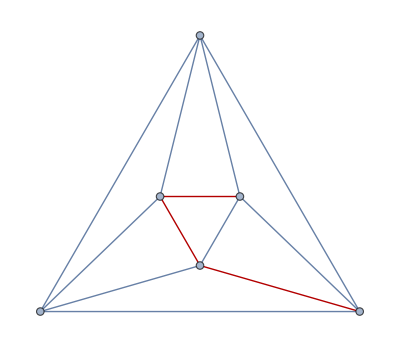
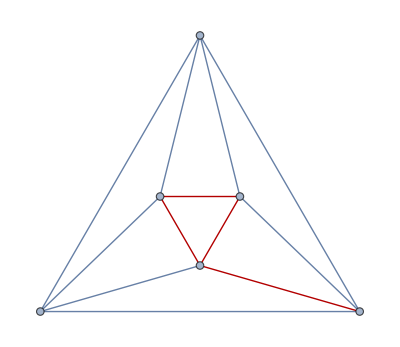
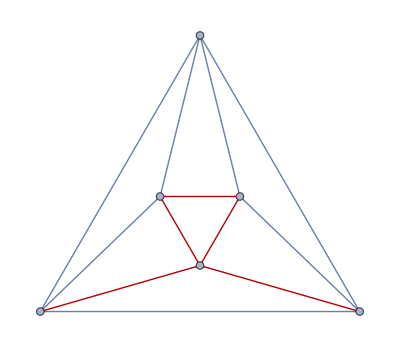
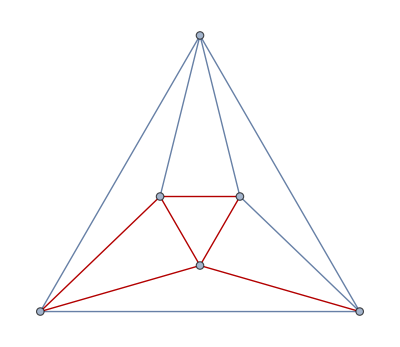
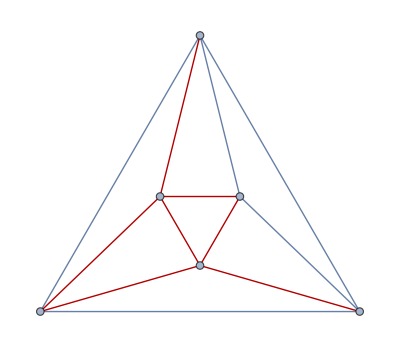
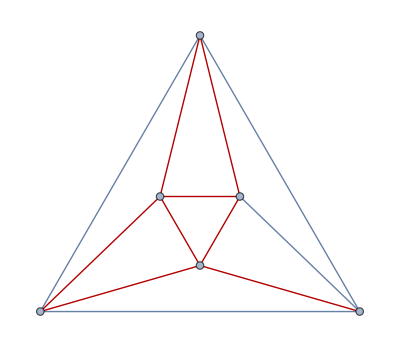

```mathematica
g=GraphData["OctahedralGraph"];
ec=FindEulerianCycle[g];
Table[HighlightGraph[g,Part[First[%],1;;i]],{i,Length[First[ec]]}]
```

```mathematica
Sum[StirlingS2[5,k],{k,1,5}]
```

52

```mathematica
BellB[5]
```

52

```mathematica
Map[{#,PrimeNu[#]}&,{210,60,36,24,16}]//tf
```

210 | 4
60 | 3
36 | 2
24 | 2
16 | 1

```mathematica
Table[Binomial[n,k],{n,0,6},{k,0,n}]//tf
```

1 |  |  |  |  |  | 
1 | 1 |  |  |  |  | 
1 | 2 | 1 |  |  |  | 
1 | 3 | 3 | 1 |  |  | 
1 | 4 | 6 | 4 | 1 |  | 
1 | 5 | 10 | 10 | 5 | 1 | 
1 | 6 | 15 | 20 | 15 | 6 | 1

```mathematica
Table[StirlingS2[n,k],{n,0,5},{k,0,n}]//tf
```

1 |  |  |  |  | 
0 | 1 |  |  |  | 
0 | 1 | 1 |  |  | 
0 | 1 | 3 | 1 |  | 
0 | 1 | 7 | 6 | 1 | 
0 | 1 | 15 | 25 | 10 | 1

```mathematica
nnFactorList[2730+1260]
```

{{3990},{2,1995},{6,665},{3,1330},{133,30},{15,266},{5,798},{10,399},{19,210},{38,105},{35,114},{57,70},{7,570},{14,285},{95,42},{21,190},{2,3,665},{2,15,133},{2,5,399},{2,19,105},{2,57,35},{2,7,285},{2,21,95},{5,6,133},{3,10,133},{3,5,266},{19,6,35},{3,19,70},{3,38,35},{7,6,95},{3,7,190},{3,14,95},{7,19,30},{19,14,15},{7,38,15},{5,19,42},{19,10,21},{5,38,21},{5,7,114},{7,10,57},{5,14,57},{2,3,5,133},{2,3,19,35},{2,3,7,95},{2,7,19,15},{2,5,19,21},{2,5,7,57},{5,7,19,6},{3,7,19,10},{3,5,19,14},{3,5,7,38},{2,3,5,7,19}}

## tmp-4

```mathematica
Module[{n,s},
n=4;
Table[
s=k+1;
Table[
{{j,s++},{j,s}} ,
{j,k,1,-1}
],
{k,1,n}]
]//tf
```

1 | 2
1 | 3 |  |  | 
2 | 3
2 | 4 | 1 | 4
1 | 5 |  | 
3 | 4
3 | 5 | 2 | 5
2 | 6 | 1 | 6
1 | 7 | 
4 | 5
4 | 6 | 3 | 6
3 | 7 | 2 | 7
2 | 8 | 1 | 8
1 | 9

```mathematica
nnListPrimeSignaturesPQ[n_]:=Module[{s},
Table[
s=k+1;
Table[
{{Prime[j],Prime[s++]},{Prime[j],Prime[s]}} ,
{j,k,1,-1}
],
{k,1,n}]
]
```

```mathematica
Map[#&,Flatten[nnListPrimeSignaturesPQ[4],2]]
Map[Times@@#&,Flatten[nnListPrimeSignaturesPQ[4],2]]
Map[Times@@#&,Flatten[nnListPrimeSignaturesPQ[4],2]]//Sort
```

{{2,3},{2,5},{3,5},{3,7},{2,7},{2,11},{5,7},{5,11},{3,11},{3,13},{2,13},{2,17},{7,11},{7,13},{5,13},{5,17},{3,17},{3,19},{2,19},{2,23}}

{6,10,15,21,14,22,35,55,33,39,26,34,77,91,65,85,51,57,38,46}

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,65,77,85,91}

```mathematica
nnListPrimeSignaturesPQ[4]//tf
```

2 | 3
2 | 5 |  |  | 
3 | 5
3 | 7 | 2 | 7
2 | 11 |  | 
5 | 7
5 | 11 | 3 | 11
3 | 13 | 2 | 13
2 | 17 | 
7 | 11
7 | 13 | 5 | 13
5 | 17 | 3 | 17
3 | 19 | 2 | 19
2 | 23

```mathematica
nnPqQ[n_]:=Module[
{ls},
ls=FactorInteger[n];
Length[ls]==2&&ls[[1,2]]==1&&ls[[2,2]]==1
]
```

```mathematica
MapIndexed[Flatten[{#2,#1}]&,Select[Table[k,{k,100}],nnPqQ]]//tf
```

1 | 6
2 | 10
3 | 14
4 | 15
5 | 21
6 | 22
7 | 26
8 | 33
9 | 34
10 | 35
11 | 38
12 | 39
13 | 46
14 | 51
15 | 55
16 | 57
17 | 58
18 | 62
19 | 65
20 | 69
21 | 74
22 | 77
23 | 82
24 | 85
25 | 86
26 | 87
27 | 91
28 | 93
29 | 94
30 | 95

```mathematica
nnListPrimeSignaturesPQ[10]//tf
```

2 | 3
2 | 5 |  |  |  |  |  |  |  |  | 
3 | 5
3 | 7 | 2 | 7
2 | 11 |  |  |  |  |  |  |  | 
5 | 7
5 | 11 | 3 | 11
3 | 13 | 2 | 13
2 | 17 |  |  |  |  |  |  | 
7 | 11
7 | 13 | 5 | 13
5 | 17 | 3 | 17
3 | 19 | 2 | 19
2 | 23 |  |  |  |  |  | 
11 | 13
11 | 17 | 7 | 17
7 | 19 | 5 | 19
5 | 23 | 3 | 23
3 | 29 | 2 | 29
2 | 31 |  |  |  |  | 
13 | 17
13 | 19 | 11 | 19
11 | 23 | 7 | 23
7 | 29 | 5 | 29
5 | 31 | 3 | 31
3 | 37 | 2 | 37
2 | 41 |  |  |  | 
17 | 19
17 | 23 | 13 | 23
13 | 29 | 11 | 29
11 | 31 | 7 | 31
7 | 37 | 5 | 37
5 | 41 | 3 | 41
3 | 43 | 2 | 43
2 | 47 |  |  | 
19 | 23
19 | 29 | 17 | 29
17 | 31 | 13 | 31
13 | 37 | 11 | 37
11 | 41 | 7 | 41
7 | 43 | 5 | 43
5 | 47 | 3 | 47
3 | 53 | 2 | 53
2 | 59 |  | 
23 | 29
23 | 31 | 19 | 31
19 | 37 | 17 | 37
17 | 41 | 13 | 41
13 | 43 | 11 | 43
11 | 47 | 7 | 47
7 | 53 | 5 | 53
5 | 59 | 3 | 59
3 | 61 | 2 | 61
2 | 67 | 
29 | 31
29 | 37 | 23 | 37
23 | 41 | 19 | 41
19 | 43 | 17 | 43
17 | 47 | 13 | 47
13 | 53 | 11 | 53
11 | 59 | 7 | 59
7 | 61 | 5 | 61
5 | 67 | 3 | 67
3 | 71 | 2 | 71
2 | 73

```mathematica
2^8 3^7
Divisors[2^8 3^7]//Length
```

559872

72

```mathematica
3^7 2^2 5^2
Divisors[3^7 2^2 5^2]//Length
```

218700

72

```mathematica
2^8 3^3 5^1
Divisors[2^8 3^3 5^1]//Length
```

34560

72

```mathematica
2^5 3^2 5^1 7^1
Divisors[2^5 3^2 5^1 7^1]//Length
```

10080

72

```mathematica
Divisors[2^5 3^2 5^1 7^1]//Length
```

72

```mathematica
2^2 3^2 5 7 11
Divisors[2^2 3^2 5 7 11]//Length
```

13860

72

```mathematica
2^7 3^2 5^2
Divisors[2^7 3^2 5^2]//Length
```

28800

72

```mathematica
nnFactorList[2^3 3^2]//Length
nnFactorList[2^3 5^2]//Length
```

16

16

```mathematica
lLet={p,q,r,s,t,u,v,w,x,y,z};
Map[#&,nnFactorList[72]]-1
lst=Map[Sort[#,#1>#2&]&,Map[#&,nnFactorList[72]]-1]
```

{{71},{1,35},{3,17},{8,7},{2,23},{5,11},{1,1,17},{1,3,8},{1,2,11},{1,5,5},{2,3,5},{2,2,7},{1,1,1,8},{1,1,2,5},{1,2,2,3},{1,1,1,2,2}}

{{71},{35,1},{17,3},{8,7},{23,2},{11,5},{17,1,1},{8,3,1},{11,2,1},{5,5,1},{5,3,2},{7,2,2},{8,1,1,1},{5,2,1,1},{3,2,2,1},{2,2,1,1,1}}

```mathematica
Map[Sort[#,#1>#2&]&,nnFactorList[8]]
Map[Sort[#,#1>#2&]&,nnFactorList[9]]
Map[Sort[#,#1>#2&]&,nnFactorList[72]]
```

{{8},{4,2},{2,2,2}}

{{9},{3,3}}

{{72},{36,2},{18,4},{9,8},{24,3},{12,6},{18,2,2},{9,4,2},{12,3,2},{6,6,2},{6,4,3},{8,3,3},{9,2,2,2},{6,3,2,2},{4,3,3,2},{3,3,2,2,2}}

```mathematica
{{8},{4,2},{2,2,2}}
{{9},{3,3}}
{{72},{36,2},{18,4},{9,8},{24,3},{12,6},{18,2,2},{9,4,2},{12,3,2},{6,6,2},{6,4,3},{8,3,3},{9,2,2,2},{6,3,2,2},{4,3,3,2},{3,3,2,2,2}}
```

```mathematica
{{8},{4,2},{2,2,2}}
{{9},{3,3}}

{{9,8},{8,3,3},{9,4,2},{4,3,3,2},{9,2,2,2},{3,3,2,2,2}}

{{72},{24,3},{36,2},{12,6},{18,2,2},{6,6,2}}

{{18,4}, {12,3,2},{6,3,2,2}, {6,4,3}}
```

```mathematica
125 121
nnFactorList[15125]//Length
```

15125

16

```mathematica
Map[Sort[#,#1>#2&]&,nnFactorList[3]]
Map[Sort[#,#1>#2&]&,nnFactorList[7]]
Map[Sort[#,#1>#2&]&,nnFactorList[21]]
```

{{3}}

{{7}}

{{21},{7,3}}

```mathematica
Map[Sort[#,#1>#2&]&,nnFactorList[5]]
Map[Sort[#,#1>#2&]&,nnFactorList[8]]
Map[Sort[#,#1>#2&]&,nnFactorList[40]]
```

{{5}}

{{8},{4,2},{2,2,2}}

{{40},{20,2},{10,4},{8,5},{10,2,2},{5,4,2},{5,2,2,2}}

```mathematica
nnFactorList[30]//Length
```

5

```mathematica
2^3 3^2 5^2
Divisors[2^3 3^2 5^2]//Length
```

1800

36

```mathematica
2^2 3^2  5^1 7^1
Divisors[2^2 3^2 5^1 7^1]//Length
```

1260

36

```mathematica
GroupBy[nnFactorList[48],Length[#]&]
```

<|1→{{48}},2→{{2,24},{4,12},{6,8},{3,16}},3→{{2,2,12},{2,4,6},{2,3,8},{3,4,4}},4→{{2,2,2,6},{2,2,3,4}},5→{{2,2,2,2,3}}|>